Biostat 279                                                Tutorial in Mathematica                                 Spring 2021

Some sample commands in Mathematica

```mathematica
4-33
```

-29

```mathematica
matrix={{1,2},{3,4}}
```

{{1,2},{3,4}}

```mathematica
imatrix=Inverse[matrix]
```

{{-2,1},{3/2,-1/2}}

```mathematica
Eigenvalues[matrix]//N
```

{5.37228,-0.372281}

```mathematica
Eigensystem[matrix]//N
```

{{5.37228,-0.372281},{{0.457427,1.},{-1.45743,1.}}}

```mathematica
g[x_]=Sin[x]-3/x^2+Log[4*x]
```

-3/x^2+Log[4 x]+Sin[x]

```mathematica
dg[x_]=D[g[x],x]
```

6/x^3+1/x+Cos[x]

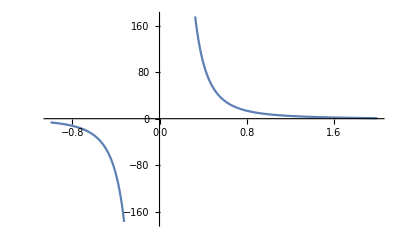

```mathematica
Plot[dg[x],{x,-1,2}]
```

```mathematica
Integrate[dg[x],x]
```

-3/x^2+Log[x]+Sin[x]

```mathematica
Integrate[g[x],{x,1,2}]//N
```

1.22904

```mathematica
Solve[x^2-3x+4==0,x]//N
```

{{x→1.5-1.32288 ⅈ},{x→1.5+1.32288 ⅈ}}

If you wish to numerically solve two equations simultaneously, do this

```mathematica
Solve[{x^2-3x+4==0,y^2-x+2==0},{x,y}]//N
```

{{x→1.5-1.32288 ⅈ,y→-0.676097+0.978318 ⅈ},{x→1.5-1.32288 ⅈ,y→0.676097-0.978318 ⅈ},{x→1.5+1.32288 ⅈ,y→-0.676097-0.978318 ⅈ},{x→1.5+1.32288 ⅈ,y→0.676097+0.978318 ⅈ}}

Now apply some of the above commands to find optimal designs and use them to confirm their optimality.  To fix ideas, consider simple linear

regression on the design space [-1,1].  The first two commands below define the regression function f(x) and f(x)f(x)’

```mathematica
f[x_]={1,x}
```

{1,x}

```mathematica
m[x_]=Outer[Times,f[x],f[x]]
```

{{1,x},{x,x^2}}

Calculate information matrix for the design equally weight at the extreme ends of the design space.

```mathematica
i=.5 m[1]+.5m[-1]
```

{{1.,0.},{0.,1.}}

```mathematica
ii=Inverse[i]
```

{{1.,0.},{0.,1.}}

Use the equivalence theorem or checking condition for D-optimality. This means the so called sensitivity function below should be bounded above by 0 with equality at the support points of the optimal design

```mathematica
c[x_]=Simplify[f[x].ii.f[x]-2]
```

-1.+1. x^2

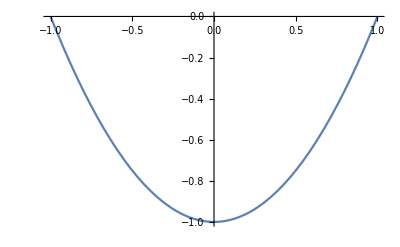

```mathematica
Plot[c[x],{x,-1,1}]
```

So above plot confirms the design equally supported at -1 and 1 is D-optimal.  Now suppose the design space is X=[2,5]; is the design equally support at 2 and 5 still D-optimal? Repeat the calculation:

```mathematica
f[x_]={1,x}
```

{1,x}

```mathematica
m[x_]=Outer[Times,f[x],f[x]]
```

{{1,x},{x,x^2}}

```mathematica
ia=m[2]/2+m[5]/2
```

{{1,7/2},{7/2,29/2}}

```mathematica
iai=Inverse[ia]//N
```

{{6.44444,-1.55556},{-1.55556,0.444444}}

```mathematica
ca[x_]=f[x].iai.f[x]-2
```

4.44444-1.55556 x+(-1.55556+0.444444 x) x

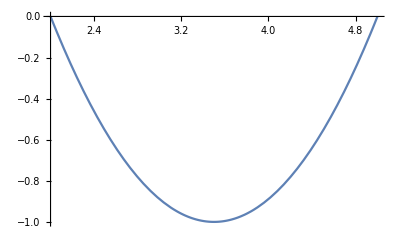

```mathematica
Plot[ca[x],{x,2,5}]
```

So answer is yes; D-optimal design on [2,5] is equally supported at 2 and 5

Below example shows A-optimal designs do not have such an ‘invariance’ property

First easy to verify that the design equally supported at -1 and 1 is also A-optimal during the

following checking conditions for A-optimality. [recall ii is the inverse of the identity matrix]

```mathematica
cao[x_]=Simplify[f[x].ii.ii.f[x]-Tr[ii]]
```

-1.+1. x^2

Now compute informatrix matrix for the design equally supported at 2 and 5; its information matrix is

```mathematica
i25=m[2]/2+m[5]/2
```

{{1,7/2},{7/2,29/2}}

```mathematica
ii25=Inverse[i25]
```

{{58/9,-14/9},{-14/9,4/9}}

```mathematica
ca25[x_]=Simplify[f[x].ii25.ii25.f[x]-Tr[ii25]]
```

2/81 (1501-868 x+106 x^2)

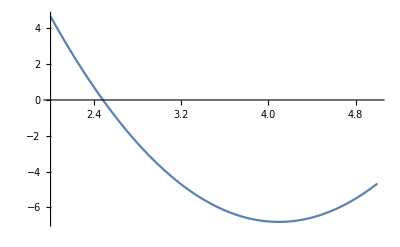

```mathematica
Plot[ca25[x],{x,2,5}]
```

The conditions of the equivalence theorem are violated and so the design equally supported at 2 and 5 is not A-optimal. So one cannot simply ‘pushes’ an optimal design linearly to a different interval.  To find the A-optimal design, you may first guess that it may not be equally weighted at the 2 extreme points, which is the next simple next step.  To this end,  let

```mathematica
i52[p_]=m[2] p+(1-p) m[5]
```

{{1,5 (1-p)+2 p},{5 (1-p)+2 p,25 (1-p)+4 p}}

```mathematica
ii52[p_]=Inverse[i52[p]]
```

{{(25 (1-p)+4 p)/(9 p-9 p^2),(-5 (1-p)-2 p)/(9 p-9 p^2)},{(-5 (1-p)-2 p)/(9 p-9 p^2),1/(9 p-9 p^2)}}

```mathematica
c52[x_,p_]=Simplify[f[x].ii52[p].ii52[p].f[x]-Tr[ii52[p]]]
```

(-189 p^3+26 (-5+x)^2+9 p^2 (97-14 x+x^2)-6 p (219-61 x+5 x^2))/(81 (-1+p)^2 p^2)

If indeed this is the A-optimal design, it must satisfy the conditions in the equivalence theorem. So

```mathematica
Solve[c52[5,p]==0,p]//N
```

{{p→0.695155},{p→1.78104}}

Clearly, the second solution is not admissible.

```mathematica
i52o=m[2] .695155+m[5] (1-.695155)
```

{{1.,2.91454},{2.91454,10.4017}}

```mathematica
ii52o=Inverse[i52o]
```

{{5.45385,-1.52815},{-1.52815,0.52432}}

```mathematica
co[x_]=Simplify[f[x].ii52o.ii52o.f[x]-Tr[ii52o]]
```

26.1015-18.2711 x+2.61015 x^2

Recalling the % sign refers to the last output, let’s plot the sensitivity function and examine its graph

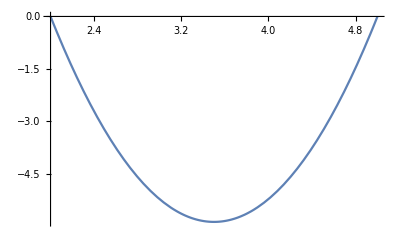

```mathematica
Plot[%,{x,2,5}]
```

We see what we want and so the design supported at 2 and 5 with weight 0.695155 at 2 is A-optimal.

Next, consider efficiencies defined in class for uniform designs.  If we have a simple linear model and u5 denotes a design equally supported at 5 points equally spaced across the design space,its information matrix and the determinant of this matrix, are respectively given by

```mathematica
u5=(m[1]+m[-1]+m[.5]+m[-.5]+m[0])/5
```

{{1,0.},{0.,0.5}}

```mathematica
Det[u5]
```

0.5

Various efficiencies of u5 or more generally, other types of designs can now be computed directly from the definitions given in class.